```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.3,Jtwo,0.3,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.5916079783099615}]
```

{z→0.591608}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.3,l->0.3}
```

0.591608+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.5916079783099615]]
```

{{0.005,0.598404},{0.01,0.605018},{0.015,0.611447},{0.02,0.617686},{0.025,0.623732},{0.03,0.629578},{0.035,0.635218},{0.04,0.640644},{0.045,0.645849},{0.05,0.650822},{0.055,0.655556},{0.06,0.660038},{0.065,0.664258},{0.07,0.668205},{0.075,0.671867},{0.08,0.675233},{0.085,0.67829},{0.09,0.68103},{0.095,0.683443},{0.1,0.685519}}

```mathematica
moduler[Lister[-1,-0.005,0.5916079783099615]]
```

{{-0.005,0.584632},{-0.01,0.577477},{-0.015,0.570145},{-0.02,0.562635},{-0.025,0.554946},{-0.03,0.547076},{-0.035,0.539024},{-0.04,0.530785},{-0.045,0.522356},{-0.05,0.513732},{-0.055,0.504907},{-0.06,0.495873},{-0.065,0.486624},{-0.07,0.477149},{-0.075,0.467437},{-0.08,0.457478},{-0.085,0.447257},{-0.09,0.436758},{-0.095,0.425963},{-0.1,0.414851}}

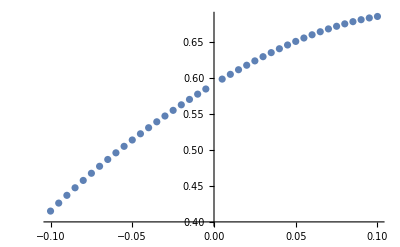

```mathematica
P = ListPlot[{{0.005,0.5984041456594782},{0.01,0.6050181189593666},{0.015,0.6114468152454415},{0.02,0.6176863161060093},{0.025,0.6237318510342424},{0.03,0.6295777840717642},{0.035,0.6352176068384775},{0.04,0.6406439416482907},{0.045,0.6458485590171534},{0.05,0.6508224144113408},{0.055,0.6555557094367287},{0.06,0.6600379827081977},{0.065,0.6642582351787698},{0.07,0.6682050935809235},{0.075,0.6718670136859205},{0.08,0.6752325222500384},{0.085,0.6782904928563043},{0.09,0.6810304466361847},{0.095,0.6834428645455508},{0.1,0.6855194941397241},{-0.005,0.5846318818228404},{-0.01,0.577477319130168},{-0.015,0.5701449642445784},{-0.02,0.5626347109092238},{-0.025,0.5549456756383598},{-0.03,0.547076194064922},{-0.035,0.5390238095457444},{-0.04,0.5307852529340903},{-0.045,0.5223564123041309},{-0.05,0.5137322912098093},{-0.055,0.5049069537589116},{-0.06,0.4958734543714051},{-0.065,0.4866237495386631},{-0.07,0.47714858816698696},{-0.075,0.46743737611575303},{-0.08,0.45747800924213067},{-0.085,0.44725666751654847},{-0.09,0.4367575603940993},{-0.095,0.4259626103465072},{-0.1,0.41485105686930057}}]
```

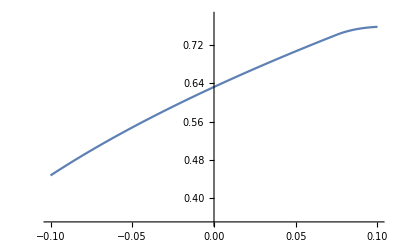

```mathematica
G = Plot[Sqrt[1+2*(0.3*Cos[Inv[0.3,Jtwo]]+Jtwo*Cos[2*Inv[0.3,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.35,0.78}]
```

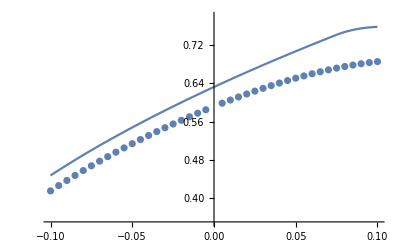

```mathematica
Show[G,P]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
differ[-1,0.3,moduler[Lister[-1,-0.005,0.5916079783099615]]]
```

{{-0.005,0.0398679},{-0.01,0.0389641},{-0.015,0.0381313},{-0.02,0.0373653},{-0.025,0.0366623},{-0.03,0.036019},{-0.035,0.0354325},{-0.04,0.0349002},{-0.045,0.03442},{-0.05,0.0339903},{-0.055,0.0336095},{-0.06,0.0332768},{-0.065,0.0329915},{-0.07,0.0327534},{-0.075,0.0325626},{-0.08,0.0324199},{-0.085,0.0323265},{-0.09,0.032284},{-0.095,0.032295},{-0.1,0.0323625}}

```mathematica
differ[1,0.3,moduler[Lister[1,0.005,0.5916079783099615]]]
```

{{0.005,0.0419083},{0.01,0.043056},{0.015,0.044297},{0.02,0.0456386},{0.025,0.0470885},{0.03,0.0486552},{0.035,0.0503479},{0.04,0.0521764},{0.045,0.0541514},{0.05,0.0562844},{0.055,0.0585871},{0.06,0.0610723},{0.065,0.0637528},{0.07,0.0666418},{0.075,0.651009},{0.08,0.0722633},{0.085,0.0735699},{0.09,0.073953},{0.095,0.0736291},{0.1,0.0727681}}

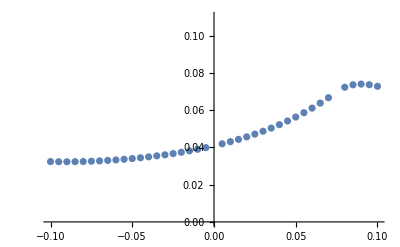

```mathematica
ListPlot[{{-0.005,0.039867918016999404},{-0.01,0.03896408116672967},{-0.015,0.03813128878524352},{-0.02,0.03736528909077619},{-0.025,0.036662302671601754},{-0.03,0.03601899541960807},{-0.035,0.03543245510805859},{-0.04,0.034900172015147835},{-0.045,0.03442002397887134},{-0.05,0.03399026629535684},{-0.055,0.03360952695453889},{-0.06,0.033276807841513045},{-0.065,0.03299149273200014},{-0.07,0.03275336319229155},{-0.075,0.032562623884246966},{-0.08,0.03241993931450493},{-0.085,0.032326484814723444},{-0.09,0.03228401558824362},{-0.095,0.03229495914907676},{-0.1,0.0323625386306573},{0.005,0.041908278083806705},{0.01,0.04305595088141945},{0.015,0.044297037184758525},{0.02,0.045638641965070725},{0.025,0.04708854221569447},{0.03,0.04865521424076258},{0.035,0.050347853201626935},{0.04,0.05217638137926017},{0.045,0.05415144098284652},{0.05,0.05628436677520676},{0.055,0.05858713341755628},{0.06,0.061072272384600224},{0.065,0.06375275374928202},{0.07,0.06664182925402995},{0.075,0.6510086418463749},{0.08,0.07226329713626423},{0.085,0.07356994475632794},{0.09,0.07395299689089019},{0.095,0.07362905722730295},{0.1,0.07276805026543087}}]
```